Ground state potentials for ^133 Cs_2

Singlet State:
The singlet potential of Coxon and Hajigeorgiou [J. Chem. Phys. 132, 094105 (2010)] is based on the MLR-model of [J. Chem. Phys. 131, 204309 (2009)]. The relevant equations to construct the potential are as follows:

V_MLR3(r) = D_e[1-(u_LR(r))/(u_LR(r_e))e^(-ϕ_MLR3(r) y_(p,a)(r,r_e))]^2-D_e
u_LR(r) = -C_6/r^6-C_8/r^8-C_10/r^10
y_(p,a)(r,r_e) =((r^p-r_e^p)/(r^p+a r_e^p))
ϕ_MLR3(r) = [1-y_m(r,r_ref)]∑_(i=0)^N ϕ_i(y_q(r,r_ref))^i+ y_m(r,r_ref)ϕ(∞)
y_m(r,r_e) = ((r^m-r_e^m)/(r^m+r_e^m))
ϕ(∞) = ln((2 D_e)/(u_LR(r_e)))

Here, D_e is the well depth of the potential, r_e is the equilibrium distance, and C_i's are the dispersion coefficients. r_ref, p, q, m, a are parameters of the potential.

Energies in cm^-1, lengths in Å

```mathematica
p = 5;
m = 6;
q = 4;
a = 1.79;
re = 4.6479723;
De = 3649.847;
C6 = 3.315*10^7;
C8 = 1.29962*10^9;
C10 = 5.136 * 10^10;
massCs = 132.905451933;
rmin = 3.1;
rmax = 20.1;
ref = 5.47;
ϕcfs = {-2.48715027, -0.7250527, -1.988236, -0.671755, -1.202501, -0.02015, -0.5414, 0.2298, 1.3964, 0.687, -8.655, 1.73, 32.2, -2.66, -61.0, 6.1, 65.6, -2.0, -28.0};
```

```mathematica
Length[ϕcfs]
```

19

```mathematica
uLR[r_]:= C6/r^6+C8/r^8+C10/r^10;
ypa[r_]:= (r^p- re^p)/(r^p + a re^p);
ym[r_]:= (r^m- re^m)/(r^m + re^m);
yq[r_]:= (r^q- re^q)/(r^q + re^q);
ϕinf = Log[(2 De)/uLR[re]]
ϕMLR3[r_]:= (1-ym[r])Sum[ϕcfs[[i+1]] yq[r]^i,{i,0,Length[ϕcfs]-1}]+ym[r] ϕinf
```

-1.01628

```mathematica
VMLR3[r_]:= De(1-uLR[r]/uLR[re] Exp[-ϕMLR3[r] ypa[r]])^2-De;
```

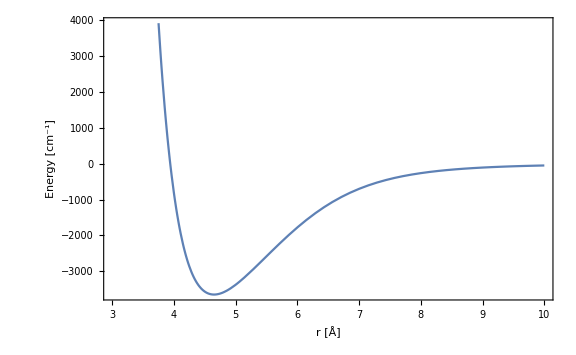

```mathematica
pSinglet = Plot[VMLR3[r],{r,3.0,10},ImageSize->Large,Frame->True,LabelStyle->Large,FrameLabel->{"r [Å]","Energy [cm^-1]"}]
```

Triplet Potential: 
Sovkov et al.  [J. Chem. Phys. 147, 104301 (2017)] employ Coxon and Hajigeorgiou’s “enhanced” MLR model to construct the triplet potential (also see errata to  paper for corrections in the m and q values).

Energies in cm^-1, lengths in Å

```mathematica
TripletDe = 279.067;
TripletRe = 6.24;
TripletRef = 6.784;
Tripleta = 2.648;
Tripletm =6;
Tripletq = 4;
Tripletp = 5;
TripletC6 = 3.31*10^7;
TripletC8 = 1.29962*10^9;
TripletC10 = 5.136 * 10^10;
Tripletϕcfs = {-2.4124,-0.2178,-0.4205,2.085, -4.192, -1.95, 1.39,1.87,-0.18,1.11};
```

```mathematica
Length[Tripletϕcfs]
```

10

```mathematica
TripletuLR[r_]:= TripletC6/r^6+TripletC8/r^8+TripletC10/r^10;
Tripletypa[r_]:= (r^Tripletp- TripletRe^Tripletp)/(r^Tripletp + Tripleta TripletRe^Tripletp);
Tripletym[r_]:= (r^Tripletm- TripletRe^Tripletm)/(r^Tripletm + TripletRe^Tripletm);
Tripletyq[r_]:= (r^Tripletq- TripletRe^Tripletq)/(r^Tripletq + TripletRe^Tripletq);
Tripletϕinf = Log[(2 TripletDe)/uLR[TripletRe]]
TripletϕMLR3[r_]:= (1-Tripletym[r])Sum[Tripletϕcfs[[i+1]] Tripletyq[r]^i,{i,0,Length[Tripletϕcfs]-1}]+Tripletym[r] Tripletϕinf
TripletVMLR3[r_]:= TripletDe(1-TripletuLR[r]/TripletuLR[TripletRe] Exp[-TripletϕMLR3[r] Tripletypa[r]])^2-TripletDe;
```

-1.11422

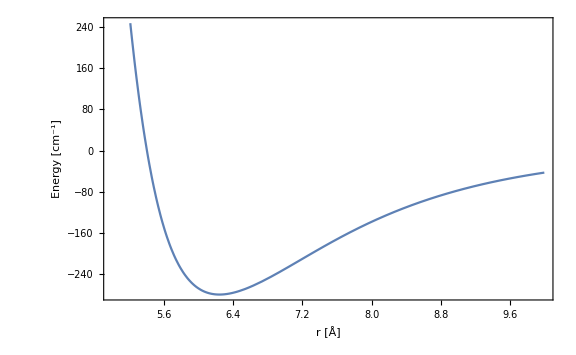

```mathematica
pTriplet =Plot[TripletVMLR3[r],{r,5.0,10},ImageSize->Large,Frame->True,LabelStyle->Large,FrameLabel->{"r [Å]","Energy [cm^-1]"}]
```

Atomic Properties of ^133 Cs

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
amu = 1822.89;
```

```mathematica
Cs133s = 1/2;
Cs133i = 7/2;
Cs133gs = 2.002319313470;
Cs133gi = -0.0003988539552;
Cs133AMHz = 2298.1579425;
Cs133μ = (massCs*amu)/2;
μbMHz = (9.27*10^-24)/(6.626*10^-34)*10^-10;
```

```mathematica
μbTHz = μbMHz *10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
```

```mathematica
Cs133ATHz = Cs133AMHz*10^-6;
Cs133Ainvcm = (Cs133ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Cs133AH =Cs133Ainvcm*invcminHartree;
```

```mathematica
Hhf[A_,i_,s_,f_,ℏ_]:= A/2 ℏ^2(f(f+1)-s(s+1)-i(i+1));
Hz[fp_,mp_,f_,m_,gi_,gs_,s_,i_,B_]:= gs μbH B √((2 fp +1)(2f +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μbH B √((2 fp +1)(2f +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
Cs133HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,3,4}],1]
```

{{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{4,-4},{4,-3},{4,-2},{4,-1},{4,0},{4,1},{4,2},{4,3},{4,4}}

```mathematica
HhfCs133Table=Table[Hhf[Cs133AH,Cs133i,Cs133s,Cs133HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,Length[Cs133HFbasis]},{jp,1,Length[Cs133HFbasis]}];
HzCs133Table[B_]= Table[Hz[Cs133HFbasis[[jp,1]],Cs133HFbasis[[jp,2]],Cs133HFbasis[[j,1]],Cs133HFbasis[[j,2]],Cs133gi,Cs133gs,Cs133s,Cs133i,B],{j,1,Length[Cs133HFbasis]},{jp,1,Length[Cs133HFbasis]}];
HCs133[B_]= HzCs133Table[B] + HhfCs133Table;
```

```mathematica
Cs133[B_]=Sort[Eigenvalues[HCs133[B]]];
```

Hyperfine and Zeeman splitting:

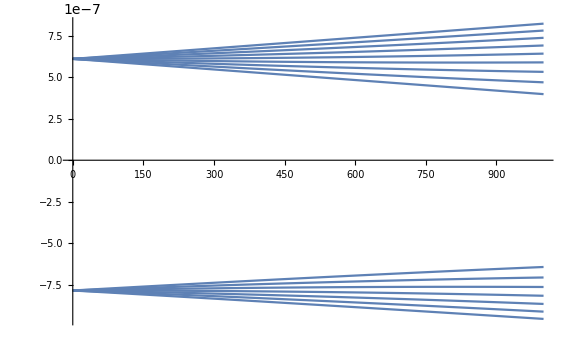

```mathematica
Plot[Cs133[B],{B,0,1000},ImageSize->Large,LabelStyle->Large]
```

Collision Problem:

```mathematica
Cs133HF2Atombasis = Flatten[Table[Table[{f1, mf1,f2,mf2},{mf1,-f1,f1},{mf2,-f2,f2}],{f1,3,4},{f2,3,4}],3];
Select[Cs133HF2Atombasis,#[[2]]+#[[4]]==6&]
```

{{3,3,3,3},{3,2,4,4},{3,3,4,3},{4,3,3,3},{4,4,3,2},{4,2,4,4},{4,3,4,3},{4,4,4,2}}

```mathematica
Cs133HF6basis = {{3,3,3,3},{3,2,4,4},{3,3,4,3},{4,2,4,4},{4,3,4,3}};
```

```mathematica
SingletProjectionSym[p_,l_]:= Table[(1/(2√((1+KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,3]]] KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[j,4]]])(1+KroneckerDelta[Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,3]]] KroneckerDelta[Cs133HF6basis[[jp,2]],Cs133HF6basis[[jp,4]]]))))*(ProjectionMatrixElement[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133s,Cs133i,0]+ProjectionMatrixElement[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133s,Cs133i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133s,Cs133i,0]+ (-1)^p(-1)^l ProjectionMatrixElement[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133s,Cs133i,0]),{j,1,5},{jp,1,5}]
```

```mathematica
Cs133SingletProjection=SingletProjectionSym[0,0]
```

```mathematica
Cs133SingletProjection={{7/64,-(√(21/2))/16,21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),(√(7/2))/16,-7/64},{-(√(21/2))/16,3/8,-3/2 √273 ((√(7/13))/48-1/(48 √91)),-(√3)/8,(√(21/2))/16},{21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),-3/2 √273 ((√(7/13))/48-1/(48 √91)),1/2 (3276 ((√(7/13))/48-1/(48 √91))^2+945 (-(√(7/15))/48-1/(48 √105))^2+1890 (-(√(7/15))/48-1/(48 √105)) ((√(7/15))/48+1/(48 √105))+945 ((√(7/15))/48+1/(48 √105))^2),3/2 √91 ((√(7/13))/48-1/(48 √91)),-21/4 √(13/2) ((√(7/13))/48-1/(48 √91))},{(√(7/2))/16,-(√3)/8,3/2 √91 ((√(7/13))/48-1/(48 √91)),1/8,-(√(7/2))/16},{-7/64,(√(21/2))/16,-21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),-(√(7/2))/16,7/64}};
Cs133TripletProjection = IdentityMatrix[5]-Cs133SingletProjection
```

```mathematica
Cs133TripletProjection={{57/64,(√(21/2))/16,-21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),-(√(7/2))/16,7/64},{(√(21/2))/16,5/8,3/2 √273 ((√(7/13))/48-1/(48 √91)),(√3)/8,-(√(21/2))/16},{-21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),3/2 √273 ((√(7/13))/48-1/(48 √91)),1+1/2 (-3276 ((√(7/13))/48-1/(48 √91))^2-945 (-(√(7/15))/48-1/(48 √105))^2-1890 (-(√(7/15))/48-1/(48 √105)) ((√(7/15))/48+1/(48 √105))-945 ((√(7/15))/48+1/(48 √105))^2),-3/2 √91 ((√(7/13))/48-1/(48 √91)),21/4 √(13/2) ((√(7/13))/48-1/(48 √91))},{-(√(7/2))/16,(√3)/8,-3/2 √91 ((√(7/13))/48-1/(48 √91)),7/8,(√(7/2))/16},{7/64,-(√(21/2))/16,21/4 √(13/2) ((√(7/13))/48-1/(48 √91)),(√(7/2))/16,57/64}};
```

```mathematica
N[MatrixForm[Cs133SingletProjection]]
```

(0.109375 | -0.202523 | 0.17539 | 0.116927 | -0.109375
-0.202523 | 0.375 | -0.32476 | -0.216506 | 0.202523
0.17539 | -0.32476 | 0.28125 | 0.1875 | -0.17539
0.116927 | -0.216506 | 0.1875 | 0.125 | -0.116927
-0.109375 | 0.202523 | -0.17539 | -0.116927 | 0.109375)

```mathematica
N[MatrixForm[Cs133TripletProjection]]
```

(0.890625 | 0.202523 | -0.17539 | -0.116927 | 0.109375
0.202523 | 0.625 | 0.32476 | 0.216506 | -0.202523
-0.17539 | 0.32476 | 0.71875 | -0.1875 | 0.17539
-0.116927 | 0.216506 | -0.1875 | 0.875 | 0.116927
0.109375 | -0.202523 | 0.17539 | 0.116927 | 0.890625)

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μB_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μB B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]+gi μB B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,3]]] KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[j,4]]])(1+KroneckerDelta[Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,3]]] KroneckerDelta[Cs133HF6basis[[jp,2]],Cs133HF6basis[[jp,4]]]))))*(HZ[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133AH,B,μbH]KroneckerDelta[Cs133HF6basis[[j,3]],Cs133HF6basis[[jp,3]]]KroneckerDelta[Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,4]]]+HZ[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133AH,B,μbH]KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[jp,1]]]KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,2]]]+(-1)^p(-1)^l HZ[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133AH,B,μbH]KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[jp,3]]]KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,4]]]+(-1)^p(-1)^l HZ[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133AH,B, μbH]KroneckerDelta[Cs133HF6basis[[j,3]],Cs133HF6basis[[jp,1]]]KroneckerDelta[Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,2]]]),{j,1,5},{jp,1,5}]
```

```mathematica
HZCs133[B_] = FullSimplify[HZsym[0,0,B]];
```

```mathematica
Rmax=400;
Rmin=1.0;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
```

```mathematica
SingletAUdat = Table[{RGrid[[i]]*AngstrominBohr,VMLR3[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletAUdat = Table[{RGrid[[i]]*AngstrominBohr,TripletVMLR3[RGrid[[i]]]*invcminHartree},{i,1,NR}];
```

```mathematica
SingletAUfun = Interpolation[SingletAUdat];
TripletAUfun = Interpolation[TripletAUdat];
```

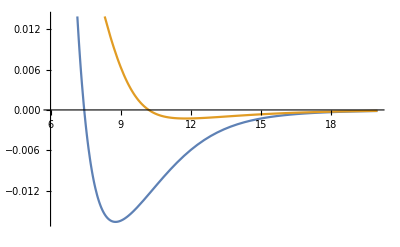

```mathematica
Plot[{SingletAUfun[r],TripletAUfun[r]},{r,6,20}]
```

```mathematica
sgdat = Import["/Users/alysonlaskowski/Alkali-Scattering/fort.10"];
tpdat = Import["/Users/alysonlaskowski/Alkali-Scattering/fort.30"];
```

```mathematica
sgfun = Interpolation[sgdat];
tpfun = Interpolation[tpdat];
```

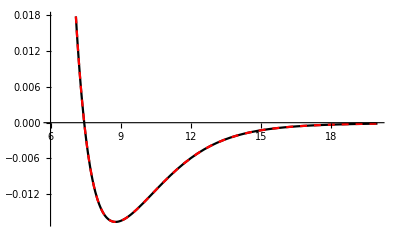

```mathematica
Plot[{SingletAUfun[r],sgfun[r]},{r,6,20},PlotStyle->{Black, {Red,Dashed}}]
```

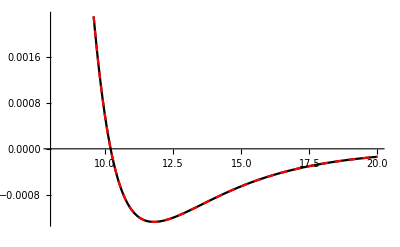

```mathematica
Plot[{TripletAUfun[r],tpfun[r]},{r,8,20},PlotStyle->{Black, {Red,Dashed}}]
```

```mathematica
HtotalCs133[B_,r_]=HZCs133[B]+ Cs133SingletProjection *SingletAUfun[r]+Cs133TripletProjection *TripletAUfun[r];
```

```mathematica
Cs133EthAU[B_] = Sort[Eigenvalues[HZCs133[B]]];
```

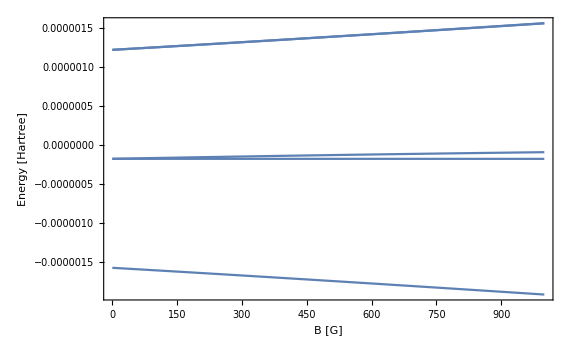

```mathematica
Plot[Cs133EthAU[B],{B,0,1000},ImageSize->Large,Frame->True,LabelStyle->Large,FrameLabel->{"B [G]","Energy [Hartree]"}]
```

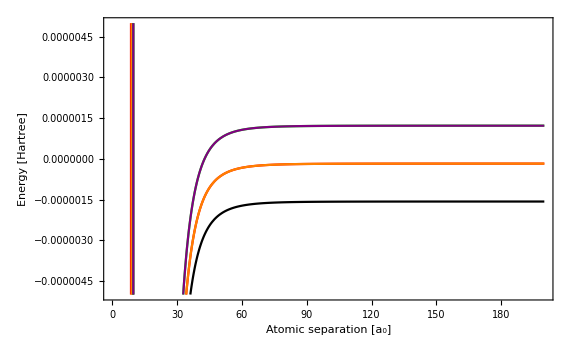

```mathematica
Plot[{ HtotalCs133[0,r][[1, 1]], HtotalCs133[0,r][[2, 2]],HtotalCs133[0,r][[3, 3]],HtotalCs133[0,r][[4, 4]],HtotalCs133[0,r][[5, 5]]},{r,3,200},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple},PlotRange->{-5*10^-6,5*10^-6}]
```

Van Der Waals Units:

```mathematica
βCs133 = 
β/.Solve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 Cs133μ β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

202.219

```mathematica
BohrinCs133vdw = 1/202.21868302499942;
Cs133vdwinHartree = 1/(2 Cs133μ βCs133^2);
HartreeinCs133vdw = 1/Cs133vdwinHartree;
```

```mathematica
C6vdw = (2 Cs133μ)/βCs133^4(C6*invcminHartree*AngstrominBohr^6)
C8vdw = (2 Cs133μ)/βCs133^6(C8*invcminHartree*AngstrominBohr^8)
C10vdw = (2 Cs133μ)/βCs133^8(C10*invcminHartree*AngstrominBohr^10)
```

0.996576

0.00341192

0.000011775

```mathematica
μbvdw = μbH*HartreeinCs133vdw;
```

```mathematica
TripletVDWdat= Table[{TripletAUdat[[i,1]]*BohrinCs133vdw, TripletAUdat[[i,2]]*HartreeinCs133vdw},{i,1,Length[TripletAUdat]}];
TripletVDW= Interpolation[TripletVDWdat(*,InterpolationOrder->1*)];
SingletVDWdat= Table[{SingletAUdat[[i,1]]*BohrinCs133vdw, SingletAUdat[[i,2]]*HartreeinCs133vdw},{i,1,Length[SingletAUdat]}];
SingletVDW= Interpolation[SingletVDWdat(*,InterpolationOrder->1*)];
```

```mathematica
Cs133vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10;
```

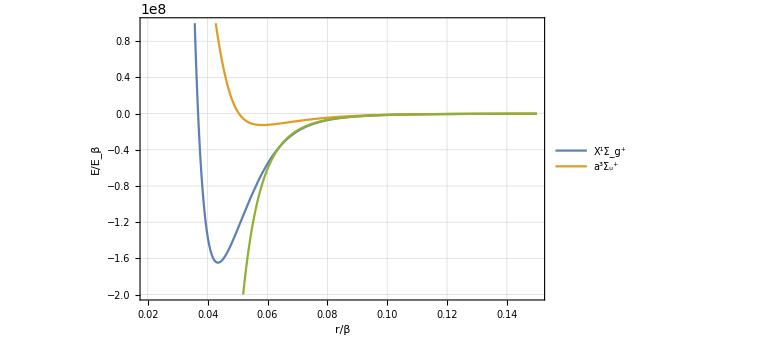

```mathematica
Plot[{SingletVDW[r],TripletVDW[r],Cs133vlr[r]},{r,0.02,0.15},PlotRange->{-2.0*10^8,10^8},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r; 
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
rx = 0.07;
rf = 3.0 ;
r0 = 0.2;
rmin = 0.03;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - Cs133vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Cs133vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Cs133vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕ=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
CalcQuantumDefect[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
f0=αfun[r0]Sin[ϕ+phaseint];
g0=-αfun[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax},AccuracyGoal->20];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
Cs133SingletQD=CalcQuantumDefect[10^-1,0,rmin,rf,r0,rx,rf,r,nr,SingletVDW,ϕ[[1]]]
```

0.226605

```mathematica
Cs133TripletQD=CalcQuantumDefect[10^-1,0,rmin,rf,r0,rx,rf,r,nr,TripletVDW,ϕ[[1]]]
```

0.443989

```mathematica
Cs133Avdw=Cs133AH*HartreeinCs133vdw;
Cs133HZVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,3]]] KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[j,4]]])(1+KroneckerDelta[Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,3]]] KroneckerDelta[Cs133HF6basis[[jp,2]],Cs133HF6basis[[jp,4]]]))))*(HZ[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133Avdw,B,μbvdw]KroneckerDelta[Cs133HF6basis[[j,3]],Cs133HF6basis[[jp,3]]]KroneckerDelta[Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,4]]]+HZ[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133Avdw,B,μbvdw]KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[jp,1]]]KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,2]]]+(-1)^p(-1)^l HZ[Cs133HF6basis[[j,3]],Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,1]],Cs133HF6basis[[jp,2]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133Avdw,B,μbvdw]KroneckerDelta[Cs133HF6basis[[j,1]],Cs133HF6basis[[jp,3]]]KroneckerDelta[Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,4]]]+(-1)^p(-1)^l HZ[Cs133HF6basis[[j,1]],Cs133HF6basis[[j,2]],Cs133HF6basis[[jp,3]],Cs133HF6basis[[jp,4]],Cs133s,Cs133i,Cs133gs,Cs133gi,Cs133Avdw,B,μbvdw]KroneckerDelta[Cs133HF6basis[[j,3]],Cs133HF6basis[[jp,1]]]KroneckerDelta[Cs133HF6basis[[j,4]],Cs133HF6basis[[jp,2]]]),{j,1,Length[Cs133HF6basis]},{jp,1,Length[Cs133HF6basis]}];
```

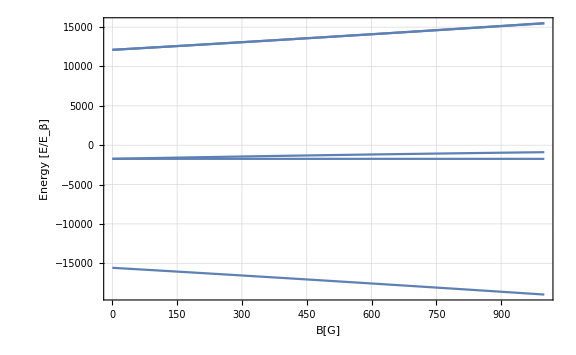

```mathematica
Cs133HZ[B_]=FullSimplify[Cs133HZVDW[0,0,B]];
Cs133HVDW[r_,B_]=Cs133HZ[B]+Cs133TripletProjection*TripletVDW[r]+Cs133SingletProjection*SingletVDW[r];
Cs133Eigensystem[B_]:= Sort[Transpose[Eigensystem[Cs133HZ[B]]]];
DD[B_]:= Transpose[{Cs133Eigensystem[B][[1]][[2]],Cs133Eigensystem[B][[2]][[2]],Cs133Eigensystem[B][[3]][[2]],Cs133Eigensystem[B][[4]][[2]],Cs133Eigensystem[B][[5]][[2]]}];
Cs133Eth[B_]:= Table[Cs133Eigensystem[B][[j]][[1]],{j,1,5}];
Plot[Cs133Eth[b],{b,0,1000},ImageSize->Large,Frame->True,GridLines->Automatic, FrameLabel->{"B[G]","Energy [E/E_β]"},LabelStyle->Large]
```

```mathematica
Eth[1000]
```

{-18972.2,-1735.59,-887.251,15480.2,15501.}